```mathematica
A={{2,0},{0,1}};B = {4,5};C=A.B
```

Set::wrsym: Symbol C is Protected.

{8,5}

```mathematica
A.B
```

{8,5}

```mathematica
First Task
```

8

First Task

```mathematica
(coord1 = {{1,1,1}, {2,2,1}, {3,1,1}}) // MatrixForm
(coord2 = {{0,0,1}, {3,2,1}, {6,0,1}}) // MatrixForm
(Q1 = Inverse[coord1]) // MatrixForm
(A = Q1.coord2) // MatrixForm
```

(1 | 1 | 1
2 | 2 | 1
3 | 1 | 1)

(0 | 0 | 1
3 | 2 | 1
6 | 0 | 1)

(-1/2 | 0 | 1/2
-1/2 | 1 | -1/2
2 | -1 | 0)

(3 | 0 | 0
0 | 2 | 0
-3 | -2 | 1)

Second Task

```mathematica
ParametricPlot3D[{v*Cos[u]^2,v*Sin[2*u],v*Cos[u]},{u,0,2π}, {v, -5,5}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{v*Cos[u]^2,2*Sqrt[1-(v*Cos[u]^2)*(v*Cos[u]^2)/(v*Cos[u])/(v*Cos[u])],v*Cos[u]},{u,0,2*π}, {v, -5,5}]
```

-Graphics3D-

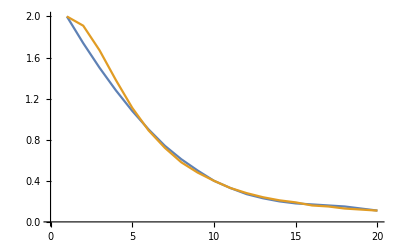

```mathematica
ListLinePlot[{{2.00,1.74,1.50,1.28,1.08,0.90,0.74,0.61,0.50,0.40,0.33,0.27,0.23,0.20,0.18,0.17,0.16,0.15,0.13,0.11}, {2.00,1.91,1.67,1.38,1.11,0.89,0.72,0.58,0.48,0.40,0.33,0.28,0.24,0.21,0.19,0.16,0.15,0.13,0.12,0.11}}]
```

```mathematica
Table[Sin[x], {x, 0, 2*Pi, Pi/6}]
```

{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}